```mathematica
files = FileNames["2efuncs*.tab"];
datas = Drop[Import[#], 1]&/@files;
ch1s=Transpose[{#[[All,1]],#[[All,2]]}]&/@datas;
ch2s=Transpose[{#[[All,1]],#[[All,3]]}]&/@datas;
data = Transpose[{ch1s, ch2s}];
fitdata = Table[Select[data[[i, 2]], #[[1]]≥ 0.0054 && #[[1]]≤0.015&], {i, 1, Length[data]}];
nlms = NonlinearModelFit[#, a - b ⅇ^(-c x), {a, b, c}, x]&/@fitdata;
funcs = Normal[#]&/@ nlms;
```

```mathematica
files
```

{}

```mathematica
Show[Plot[#[[2]], {x, 0.005, 0.016},ImageSize->500, PlotRange->All, Frame->True, PlotStyle->{Red, Dashed, Thick}], ListPlot[#[[1, 2]],PlotStyle->{PointSize[0.00001]}]]&/@ Transpose[{data, funcs}]
```

{}

```mathematica
taus=#["ParameterTableEntries"][[3, 1]]&/@ nlms
```

{1646.12,1054.16,530.827,327.232,420.066,357.267,395.675,313.834,279.119}

```mathematica
filters = {0.,0.398736,0.453891,0.816374,1.04996,1.29003,1.49831,1.65801,2.06819};
filters2 = {0,0.3,0.6,1,1.3,2,2.3,2.6,3.3};
```

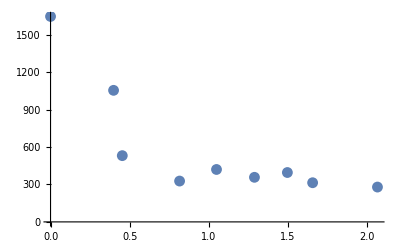

```mathematica
ListPlot[Transpose[{filters, taus}]]
```

```mathematica
taudata = Transpose[{1/10^filters, taus}]
```

{{1.,1646.12},{0.399268,1054.16},{0.351649,530.827},{0.152625,327.232},{0.0891333,420.066},{0.0512826,357.267},{0.0317461,395.675},{0.0219781,313.834},{0.00854693,279.119}}

```mathematica
taufit = NonlinearModelFit[taudata, a + b x, {a, b}, x]
```

FittedModel[269.8+1375.01 x]

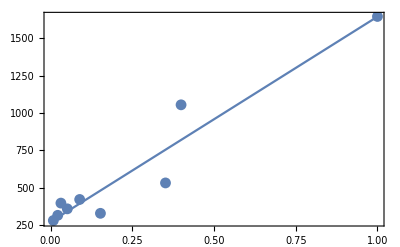

```mathematica
Show[Plot[Normal[taufit], {x, 0, 1}, Frame->True, PlotRange-> All], ListPlot[taudata]]
```

```mathematica
1/269.80036053337403
```

0.00370644